```mathematica
Get[StringJoin[NotebookDirectory[] , "article/allPrimes.mx"]]
```

```mathematica
Length/@allPrimes
```

{0,10000,10000,208192,10000,43519,10000,224427,10043,2354638,10000}

```mathematica
allPrimes=allPrimes[[2;;]];
```

```mathematica
allPrimes=allPrimes[[All,;;10000]];
```

```mathematica
fracs=Table[x/allPrimes[[k,x]],{k,10},{x,10000}];
```

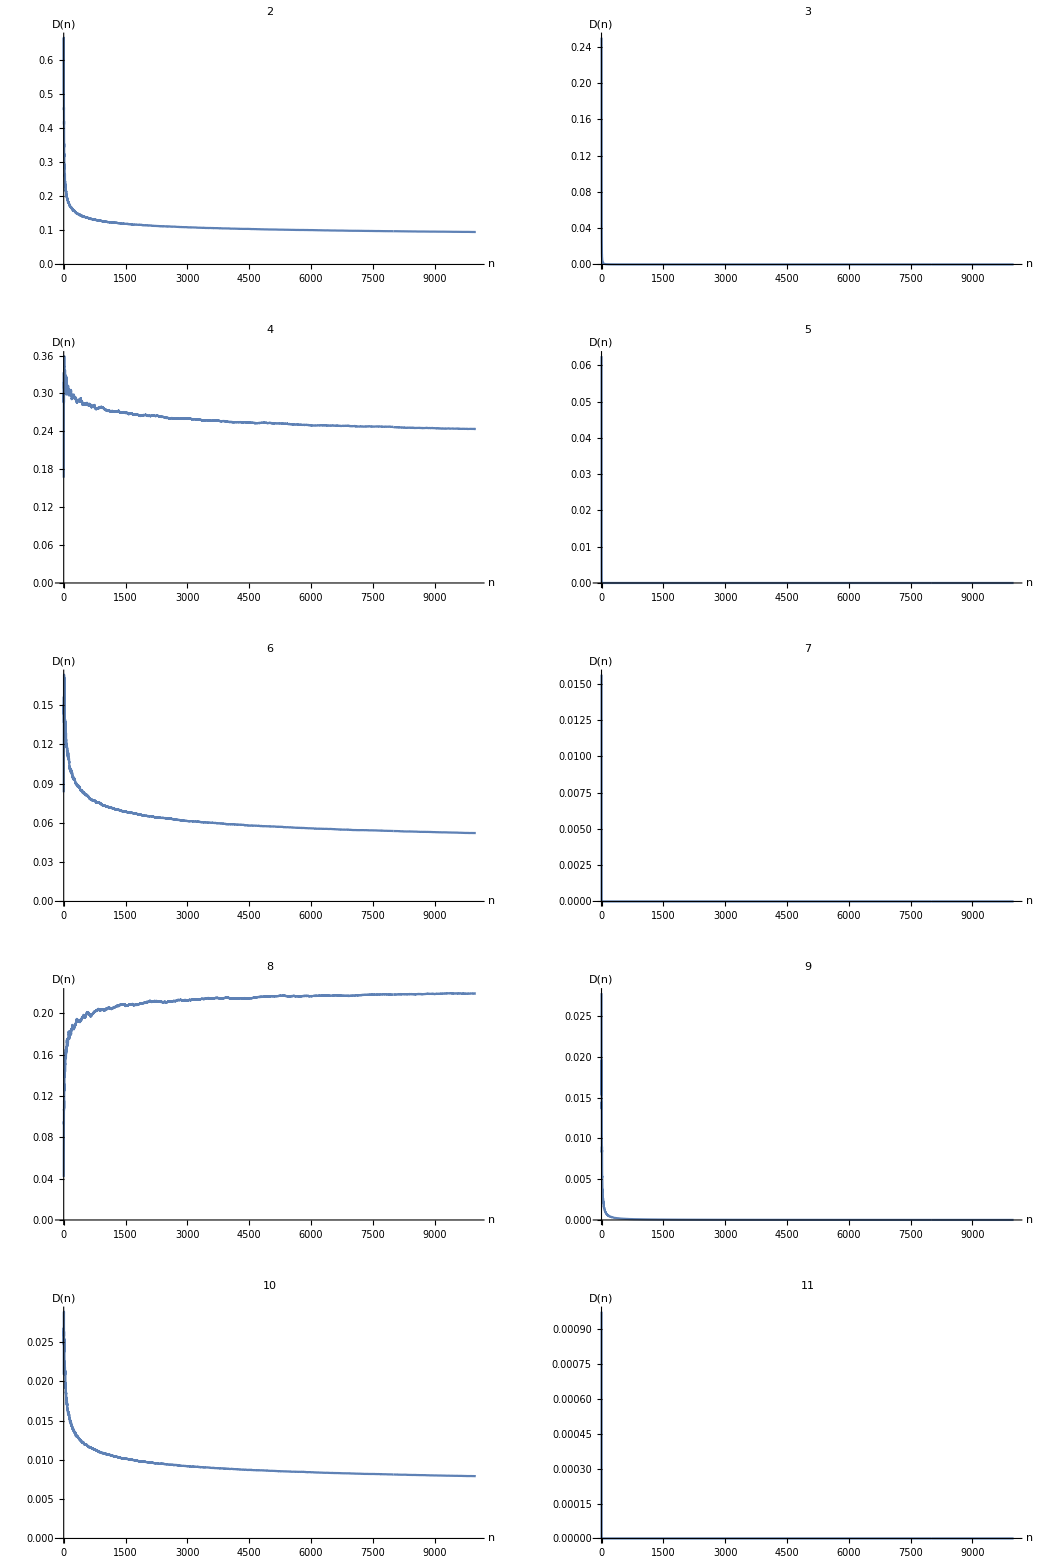

```mathematica
GraphicsGrid[Partition[Table[ListLinePlot[fracs[[x]],PlotRange->Full,PlotLabel->x+1,AxesLabel->{n,HoldForm["D"[n]]},ImageSize->Large],{x,10}],2],ImageSize->600]
```

```mathematica
Export[NotebookDirectory[]<>"counts.pdf",%%]
```

/home/blmayer/doctorate/thesis/counts.pdf

```mathematica
dens=Table[x/allPrimes[[k,x]],{k,10},{x,10000}];
```

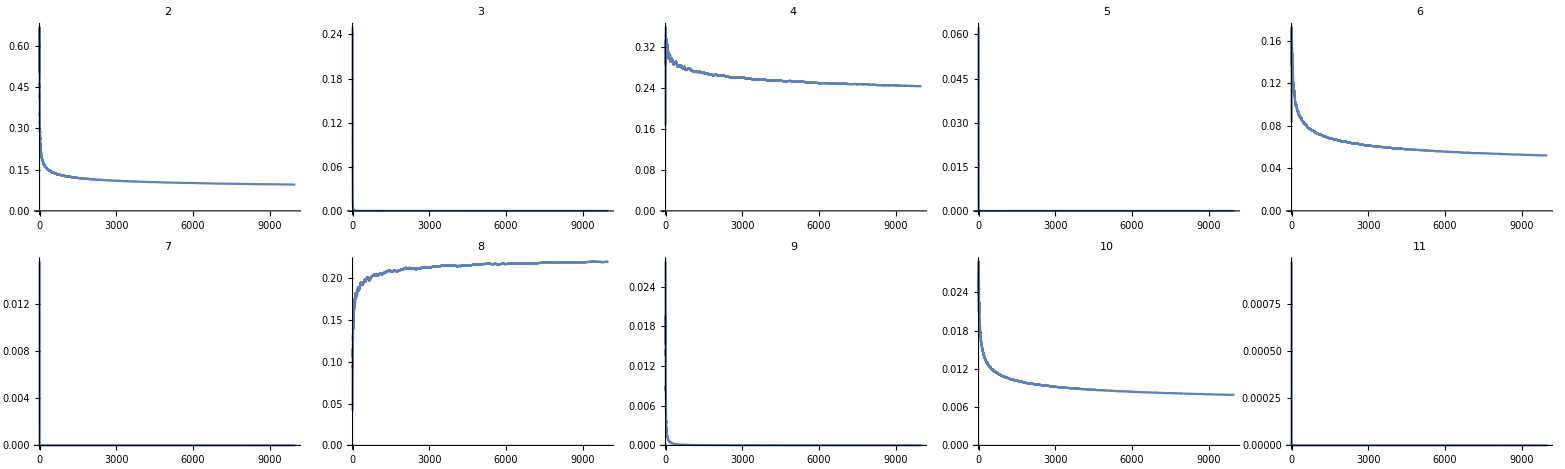
-Graphics-Prime density π(x)/x

```mathematica
Labeled[Grid[Partition[Table[ListLinePlot[dens[[x]],PlotRange->Full,PlotLabel->x+1],{x,10}],5]],"Prime density π(x)/x"]
```

```mathematica
Export["densities.pdf", %5]
```

densities.pdf